# LieART/LieART

Tools for Lie Algebras and Representation Theory

## Paclet Manifest

"CHANGELOG.md"CHANGELOG.md

"COPYING"COPYING

"COPYING.LESSER"COPYING.LESSER

"Documentation"

"English"

"Guides"

"LieART.nb"DocumentationEnglishGuidesLieART.nb

"ReferencePages"

"Symbols"

"Algebra.nb"DocumentationEnglishReferencePagesSymbolsAlgebra.nb

"CartanMatrix.nb"DocumentationEnglishReferencePagesSymbolsCartanMatrix.nb

"DecomposeIrrep.nb"DocumentationEnglishReferencePagesSymbolsDecomposeIrrep.nb

"DecomposeProduct.nb"DocumentationEnglishReferencePagesSymbolsDecomposeProduct.nb

"DimName.nb"DocumentationEnglishReferencePagesSymbolsDimName.nb

"Dim.nb"DocumentationEnglishReferencePagesSymbolsDim.nb

"HighestRoot.nb"DocumentationEnglishReferencePagesSymbolsHighestRoot.nb

"Index.nb"DocumentationEnglishReferencePagesSymbolsIndex.nb

"Irrep.nb"DocumentationEnglishReferencePagesSymbolsIrrep.nb

"IrrepPlus.nb"DocumentationEnglishReferencePagesSymbolsIrrepPlus.nb

"LaTeXForm.nb"DocumentationEnglishReferencePagesSymbolsLaTeXForm.nb

"MetricTensor.nb"DocumentationEnglishReferencePagesSymbolsMetricTensor.nb

"OrthogonalSimpleRoots.nb"DocumentationEnglishReferencePagesSymbolsOrthogonalSimpleRoots.nb

"PositiveRoots.nb"DocumentationEnglishReferencePagesSymbolsPositiveRoots.nb

"ProductAlgebra.nb"DocumentationEnglishReferencePagesSymbolsProductAlgebra.nb

"ProductIrrep.nb"DocumentationEnglishReferencePagesSymbolsProductIrrep.nb

"RootSystem.nb"DocumentationEnglishReferencePagesSymbolsRootSystem.nb

"WeightSystem.nb"DocumentationEnglishReferencePagesSymbolsWeightSystem.nb

"YoungTableau.nb"DocumentationEnglishReferencePagesSymbolsYoungTableau.nb

"Tables"

"BranchingRules.nb"DocumentationEnglishTablesBranchingRules.nb

"IrrepProperties.nb"DocumentationEnglishTablesIrrepProperties.nb

"TensorProducts.nb"DocumentationEnglishTablesTensorProducts.nb

"Tutorials"

"QuickStartTutorial.nb"DocumentationEnglishTutorialsQuickStartTutorial.nb

"Kernel"

"BranchingRules.wl"KernelBranchingRules.wl

"LieART.wl"KernelLieART.wl

"Tables.wl"KernelTables.wl

"Latex"

"lieart.sty"Latexlieart.sty

"LieART.code-workspace"LieART.code-workspace

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image



### Basic Description

LieART (Lie Algebras and Representation Theory) is a Wolfram paclet for computations frequently encountered in Lie algebras and representation theory, such as tensor product decomposition and subalgebra branching of irreducible representations.

### Details

LieART can handle all classical and exceptional Lie algebras. It computes root systems of Lie algebras, weight systems, and several other properties of irreducible representations. LieART's user interface has been created with a strong focus on usability and thus allows the input of irreducible representations via their dimensional name, while the output is in the textbook style used in most particle-physics publications. The unique Dynkin labels of irreducible representations are used internally and can also be used for input and output. LieART exploits the Weyl reflection group for most of the calculations, resulting in fast computations and low memory consumption.

### Primary Context

LieART`LieART`

### Main Guide Page

## Examples

```mathematica
<<LieART`
```

LieART 2.1.1

last revised 6 February 2025

### Basic Examples

Enter the OverBar[10] of SU(5) by its dimensional name:

```mathematica
Irrep[SU5][Bar[10]]
```

OverBar[10]

Decompose the tensor product 3⊗OverBar[3] of SU(3):

```mathematica
DecomposeProduct[Irrep[SU3][3],Irrep[SU3][Bar[3]]]
```

1+8

Decompose the OverBar[10] of SU(5) to SU(3)⊗SU(2)⊗U(1):

```mathematica
DecomposeIrrep[Irrep[SU5][Bar[10]],ProductAlgebra[SU3,SU2,U1]]
```

(1,1)(6)+(3,1)(-4)+(OverBar[3],2)(1)

### Scope

Display the root system of SU(5) in spindle shape:

```mathematica
RootSystem[A4,SpindleShape->True]
```

1 | 0 | 0 | 1
  -1 | 1 | 0 | 11 | 0 | 1 | -1
  -1 | 1 | 1 | -10 | -1 | 1 | 11 | 1 | -1 | 0
  -1 | 2 | -1 | 00 | -1 | 2 | -10 | 0 | -1 | 22 | -1 | 0 | 0
  0 | 0 | 0 | 00 | 0 | 0 | 00 | 0 | 0 | 00 | 0 | 0 | 0
  -2 | 1 | 0 | 00 | 0 | 1 | -20 | 1 | -2 | 11 | -2 | 1 | 0
  -1 | -1 | 1 | 00 | 1 | -1 | -11 | -1 | -1 | 1
  -1 | 0 | -1 | 11 | -1 | 0 | -1
  -1 | 0 | 0 | -1

Show the Dynkin diagram of SO(7):

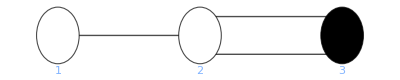

```mathematica
DynkinDiagram[SO7]
```

Weight diagram of SU(3) irrep 8:

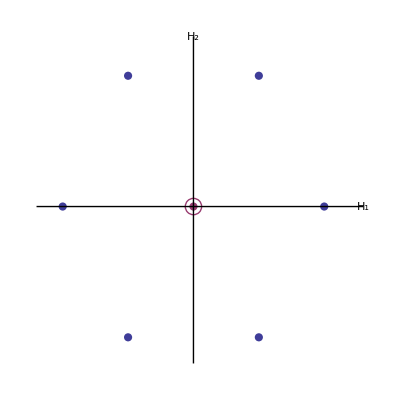

```mathematica
WeightDiagram[Irrep[SU3][8]]
```

## Source & Additional Information

### Creator

Robert Feger, Thomas Kephart and Robert Saskowski

### Source Control Repository

https://github.com/rfeger/LieART

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Lie algebra

Lie group

representation theory

irreducible representation

tensor product

branching rule

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

### Original Source References and Attributions

Robert Feger and Thomas W. Kephart.
​LieART—A Mathematica application for Lie algebras and representation theory.​
Comput.Phys.Commun. 192 (2015), 166-195
DOI: 10.1016/j.cpc.2014.12.023​
e-Print: 1206.6379 [math-ph]

Robert Feger, Thomas W. Kephart and Robert J. Saskowski.
​LieART 2.0 – A Mathematica application for Lie Algebras and Representation Theory.
​Comput.Phys.Commun. 257 (2020), 107490
DOI: 10.1016/j.cpc.2020.107490​
e-Print: 1912.10969 [hep-th]

### Links

Wolfram Community: LieART

Wolfram R&D Live: LieART

### Compatibility

#### Wolfram Language Version

11.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.